```mathematica
f[a_Integer]:={ToString[a],RandomInteger[10,a]}
d[{r__}]:=({r})/.x_Integer:>f[x]
f[{r__},n_]:=Nest[d,{r},n]

 {1,2,3}/.x_Integer:>f[x]
```

{{1,{9}},{2,{6,2}},{3,{4,9,2}}}

```mathematica
a[{x__}]:=x^2+1
```

```mathematica
({##}/.x_Integer:>f[x])&@@{1,2,3}
```

```mathematica
{{"1",{2}},{"2",{2,0}},{"3",{1,9,3}}}/. x_String:> ToExpression[x]
```

```mathematica
{{1,{2}},{2,{2,0}},{3,{1,9,3}}}
```

{{1,{2}},{2,{2,0}},{3,{1,9,3}}}

```mathematica
{{"1",{2}},{"2",{2,0}},{"3",{1,9,3}}}
```

```mathematica
{{"1",{2}},{"2",{2,0}},{"3",{1,9,3}}}
```

{{1,{2}},{2,{2,0}},{3,{1,9,3}}}

```mathematica
"2"/. String->Symbol

"Ismail"
```

2

Ismail

```mathematica
ToCharacterCode@Characters["Ismail abdla"]
```

{{73},{115},{109},{97},{105},{108},{32},{97},{98},{100},{108},{97}}

```mathematica
FromCharacterCode[{{73},{115},{109},{97},{105},{108},{32},{97},{98},{100},{108},{97}}]
```

{I,s,m,a,i,l, ,a,b,d,l,a}

```mathematica
ToCharacterCode@{"I","s","m","a","i","l"}
```

{{73},{115},{109},{97},{105},{108}}

```mathematica
"2"
```

2

```mathematica
ToCharacterCode["2"]
```

{50}

```mathematica
ToExpression["2"]
```

2

```mathematica
"2"+1/.x_String:>ToExpression[x]
```

3

{1,2,Null}

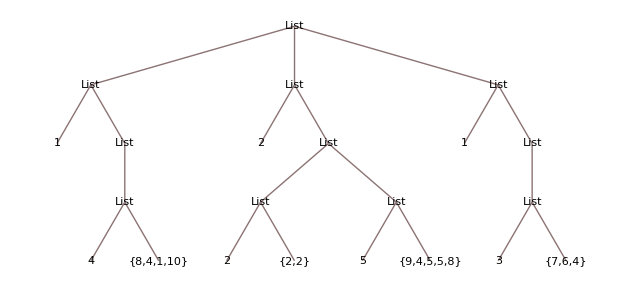

```mathematica
{1,2,Null}
```

```mathematica
b[{a_,z_}]:={z,a}
b[{R___,x_}]:=Join[{x},b[{R}]]
```

```mathematica
f1[{x___},n_]:=(Tuples[{x},n]//DeleteCases[#,{___,a_,___,a_,___}]&)
```

```mathematica
f1[{a,b},{4}]
```

{}

```mathematica
Tuples[{a,b},{4}]
```

{{a,a,a,a},{a,a,a,b},{a,a,b,a},{a,a,b,b},{a,b,a,a},{a,b,a,b},{a,b,b,a},{a,b,b,b},{b,a,a,a},{b,a,a,b},{b,a,b,a},{b,a,b,b},{b,b,a,a},{b,b,a,b},{b,b,b,a},{b,b,b,b}}

```mathematica
MatrixForm@(a{{1,2,3},{4,5,6},{7,8,9}})
```

```mathematica
r=({{a, 2 a, 3 a}, {4 a, 5 a, 6 a}, {7 a, 8 a, 9 a}})/.x_ *a->Subscript[a, x]
```

{{a,a_2,a_3},{a_4,a_5,a_6},{a_7,a_8,a_9}}

```mathematica
r={{a,Subscript[a, 2],Subscript[a, 3]},{Subscript[a, 4],Subscript[a, 5],Subscript[a, 6]},{Subscript[a, 7],Subscript[a, 8],Subscript[a, 9]}}
```

{{a,a_2,a_3},{a_4,a_5,a_6},{a_7,a_8,a_9}}

```mathematica
gg[r_]:=FindInstance[
  Unequal@@@ (And@@r)&&
Unequal@@@ (And @@Transpose[r])&&
0<Flatten[r]<10,DeleteCases[Flatten[r],_Integer],Integers]/.{x_}:>Partition[x,Sqrt@ Length@Flatten[r]]/.{(Subscript[a, _]->x_)->x,(a->x_)->x}
```

```mathematica
m=({{1, x, 3}, {2, y, 1}, {3, 1, z}})
```

{{1,x,3},{2,y,1},{3,1,z}}

```mathematica
DeleteCases[{}//Flatten,_Integer]
```

{x,y,z}

```mathematica
MatrixForm@m/.gg[m]
```

{(1 | 2 | 3
2 | 3 | 1
3 | 1 | 2)}